```mathematica
vsol=NDSolveValue[{D[u[t,x,y],{t,2}]-u[t,x,y]==0,D[v[t,x,y],t]-D[u[t,x,y],{x,2}]-D[v[t,x,y],{y,2}]==0,u[0,x,y]==-y,v[0,x,y]==x},{u[t,x,y],v[t,x,y]},{t,0,5},{x,-Pi,Pi},{y,-Pi,Pi}]
```

{InterpolatingFunction[{{0., 5.}, {-3.14159, 3.14159}, {-3.14159, 3.14159}}, <>][t,x,y],InterpolatingFunction[{{0., 5.}, {-3.14159, 3.14159}, {-3.14159, 3.14159}}, <>][t,x,y]}

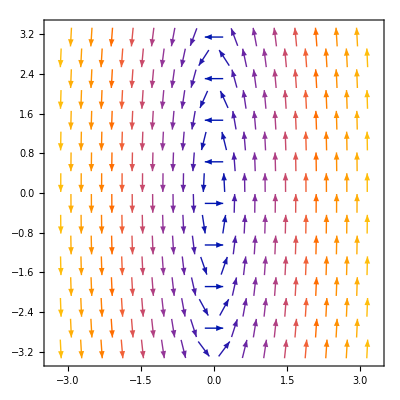

```mathematica
VectorPlot[vsol/.t->3,{x,-Pi,Pi},{y,-Pi,Pi}]
```

```mathematica
outDat=Table[Flatten[Table[vsol,{x,-Pi,Pi,2Pi/19},{y,-Pi,Pi,2Pi/19}]],{t,0,5,5/50}]
Export["C:\\Users\\Sam\\Documents\\MATLAB\\savedArrows.csv",outDat,"CSV"]
```

{{3.14159,-3.14159,2.8109,-3.14159,2.4802,-3.14159,2.14951,-3.14159,1.81882,-3.14159,1.48812,-3.14159,1.15743,-3.14159,0.826735,-3.14159,0.496041,-3.14159,0.165347,-3.14159,-0.165347,-3.14159,756,0.165347,3.14159,-0.165347,3.14159,-0.496041,3.14159,-0.826735,3.14159,-1.15743,3.14159,-1.48812,3.14159,-1.81882,3.14159,-2.14951,3.14159,-2.4802,3.14159,-2.8109,3.14159,-3.14159,3.14159},49,{1}}
 |  |  |  |

C:\Users\Sam\Documents\MATLAB\savedArrows.csv